# Javier Salazar 1001144647

## Project 2.

1. Let X be exponential with parameter  λ = 2 , density f(x ) = λe^(-λ x), EX =1/λ,  VarX =1/λ^2. 
   Plot the graph of f(x) on [0,5].

Illustrate the Central Limit Theorem (CLT) for X as follows

(a)  Simulate  X=X_1+...+ X_10  n = 100 times, use the (practical) range  0 ≤ X ≤ 20 and bin size = 1 
      Graph:  Histogram of bin counts, Frequencies, and combined Frequencies with the Normal curve from CLT on [0, 20]
      Label the three graphs appropriately    
(b)  Simulate  X=X_1+...+ X_30   n = 1000 times, use the (practical) range  0 ≤ X ≤ 30 and bin size = 1 
       Graph:  Histogram of bin counts, Frequencies, and combined Frequencies with the Normal curve from CLT on [0, 30]
       Label the three graphs appropriately      
 (c)  Simulate  X=X_1+...+ X_100   n = 10000 times, use the (practical) range  30 ≤ X ≤ 70 and bin size = 1 
       Graph:  Histogram of bin counts, Frequencies, and combined Frequencies with the Normal curve from CLT on [30, 70]
       Label the three graphs  appropriately
(c2)  Do (c) with standardization and compare the frequencies with Standard Normal N(0,1) density   1/(√(2π))ⅇ^(-x^2/2)      
       
Illustrate the Law of Large Numbers (LLN) for X exponential with parameter  λ =  1/3, EX =1/λ= 3 as follows:

(d)  Graph : all averages {X_1,(X_1+ X_2)/2,...,(X_1+...+ X_10000)/10000}, first 50 averages, averages from 5000 to 10000
(e)  Use "Do loop"  to simulate 3 different samples of (X_1+...+ X_n)/n for n = 1000000.  Take the average of the three runs
       to get a better approximation to EX      
 (f)  OPTIONAL (extra credit).  If "your computer is fast enough" try  (e)  for  n = 10^7  or  10^8 or even 10^9.

General::obspkg: BarCharts` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

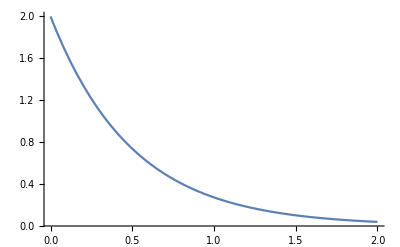

```mathematica
<<BarCharts`
Plot[2*Exp[-2*x], {x, 0, 2}, PlotRange -> All]
```

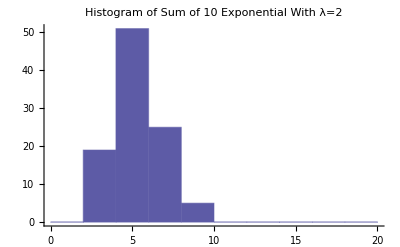

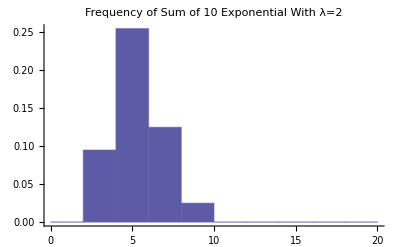

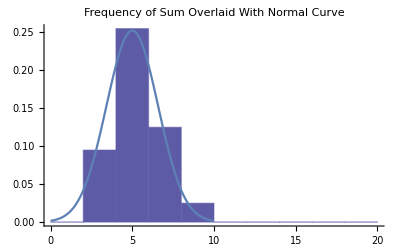

```mathematica
X:=Sum[Random[ExponentialDistribution[2]],{10}]
Sample100=Table[X,100];
bcount=BinCounts[Sample100,{0,20,2}];
GeneralizedBarChart[Table[{1+(i-1)*2,bcount[[i]],2},{i,1,10}],PlotLabel->"Histogram of Sum of 10 Exponential With λ=2"]
GeneralizedBarChart[Table[{1+(i-1)*2,bcount[[i]]/(2*100),2},{i,1,10}],PlotLabel->"Frequency of Sum of 10 Exponential With λ=2"]
Show[GeneralizedBarChart[Table[{1+(i-1)*2,bcount[[i]]/(2*100),2},{i,1,10}],PlotLabel->"Frequency of Sum Overlaid With Normal Curve"],Plot[1/√(5*Pi)*Exp[-(x-5)^2/5],{x,0,10},PlotRange->All]]
```

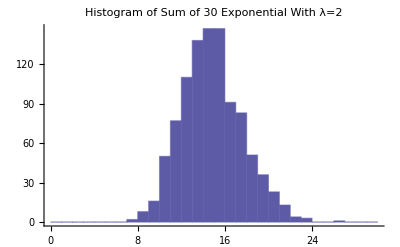

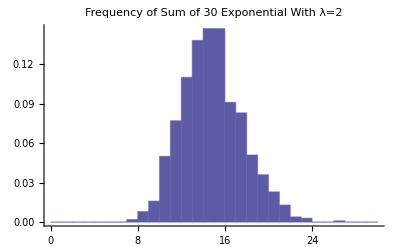

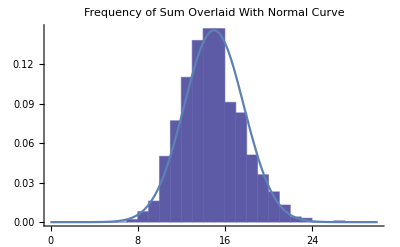

```mathematica
X:=Sum[Random[ExponentialDistribution[2]],{30}]
Sample100=Table[X,1000];
bcount=BinCounts[Sample100,{0,30,1}];
GeneralizedBarChart[Table[{.5+(i-1),bcount[[i]],1},{i,1,30}],PlotLabel->"Histogram of Sum of 30 Exponential With λ=2"]
GeneralizedBarChart[Table[{.5+(i-1),bcount[[i]]/(1*1000),1},{i,1,30}],PlotLabel->"Frequency of Sum of 30 Exponential With λ=2"]
Show[GeneralizedBarChart[Table[{.5+(i-1),bcount[[i]]/(1*1000),1},{i,1,30}],PlotLabel->"Frequency of Sum Overlaid With Normal Curve"],Plot[1/√(15*Pi)*Exp[-(x-15)^2/15],{x,0,30},PlotRange->All]]
```

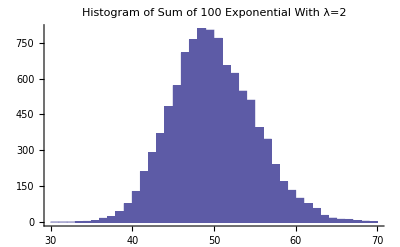

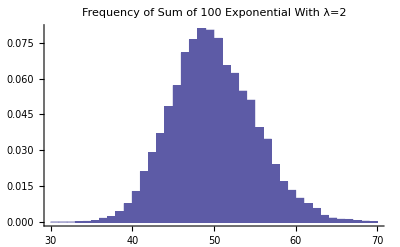

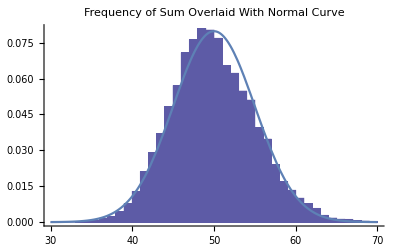

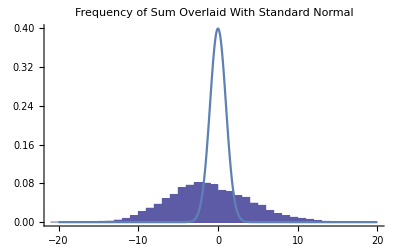

```mathematica
X:=Sum[Random[ExponentialDistribution[2]],{100}]
Sample100=Table[X,10000];
bcount=BinCounts[Sample100,{30,70,1}];
GeneralizedBarChart[Table[{30.5+(i-1),bcount[[i]],1},{i,1,40}],PlotLabel->"Histogram of Sum of 100 Exponential With λ=2"]
GeneralizedBarChart[Table[{30.5+(i-1),bcount[[i]]/(1*10000),1},{i,1,40}],PlotLabel->"Frequency of Sum of 100 Exponential With λ=2"]
Show[GeneralizedBarChart[Table[{30.5+(i-1),bcount[[i]]/(1*10000),1},{i,1,40}],PlotLabel->"Frequency of Sum Overlaid With Normal Curve"],Plot[1/√(50*Pi)*Exp[-(x-50)^2/50],{x,30,70},PlotRange->All]]
Show[GeneralizedBarChart[Table[{-20.5+(i-1),bcount[[i]]/(1*10000),1},{i,1,40}],PlotLabel->"Frequency of Sum Overlaid With Standard Normal"],Plot[1/√(2*Pi)*Exp[-x^2/2],{x,-20,20},PlotRange->All]]
```

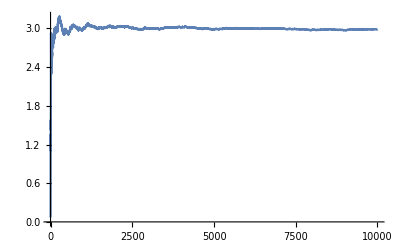

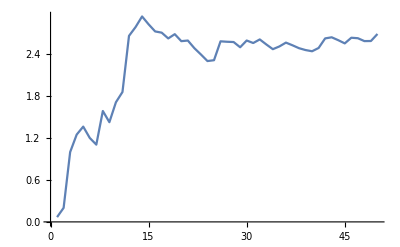

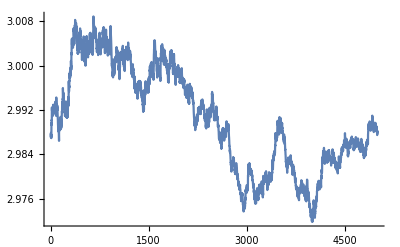

2.99799

```mathematica
data=Table[Random[ExponentialDistribution[1/3]],10000];
sumdata=Accumulate[data];
average=Table[sumdata[[i]]/i,{i,1,10000}];
ListPlot[average,Joined->True,PlotRange->All]
ListPlot[Drop[average,{51,10000}],Joined->True,PlotRange->All]
ListPlot[Drop[average,{1,5000}],Joined->True,PlotRange->All]
s=0;n=1000000;sum=0;
For[i=1,i<4,i++,Do[r=Random[ExponentialDistribution[1/3]];s=s+r,{i,1,n}];sum=sum+s;s=0]
Print[sum/n/3//N]
```

2.  Let X be Poisson with  λ = 2 , density  f(x) = λ^x/(x!)e^(-λ x), x = 0,1,2,..., EX =λ,  VarX =λ. 
     Plot the graph of f(x) on {0,1,...,15}.
     
  Illustrate the Central Limit Theorem (CLT) for X as follows:
  
(a)  Simulate  X=X_1+...+ X_10  n = 100 times, use the (practical) range  0 ≤ X ≤ 40 and bin size = 1
      Graph:  Histogram of bin counts, Frequencies, and combined Frequencies with the Normal curve from CLT on [0, 40]
      Label the three graphs  appropriately
(b)  Simulate  X=X_1+...+ X_30   n = 1000 times, use the (practical) range  30 ≤ X ≤ 90 and bin size = 1 
       Display:  Histogram of bin counts, Frequencies, and combined Frequencies with the Normal curve from CLT on [30, 90]
       Label the three graphs  appropriately    
 (c)  Simulate  X=X_1+...+ X_100   n = 10000 times, use the (practical) range  150 ≤ X ≤ 250 and bin size = 1
       Graph:  Histogram of bin counts, Frequencies, and combined Frequencies with the Normal curve from CLT on [150, 250]
       Label the three graphs appropriately
       
Illustrate the Law of Large Numbers (LLN) for X Poisson with parameter  λ = 5,  EX =λ = 5  as follows:

(d)  Graph : {X_1,(X_1+ X_2)/2,...,(X_1+...+ X_10000)/10000}, first 50 averages, averages from 5000 to 10000
(e)  Use “Do loop”  to simulate 3 different samples of (X_1+...+ X_n)/n for n = 1000000.  Take the average of the three runs
       to get a better approximation to EX
 (f)  OPTIONAL (extra credit).  If “your computer is fast enough” try  (e)  for  n = 10^7  or  10^8 or even 10^9.
  (* Do loop *)   s = 0; n = 1000000; Do[r = random distribution of choice ; s = s + r, {i, 1, n}]; Print[s/n//N]

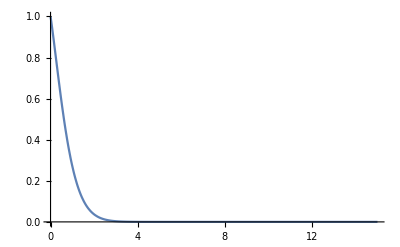

```mathematica
Plot[2^x/x!*Exp[-2*x], {x, 0, 15}, PlotRange -> All]
```

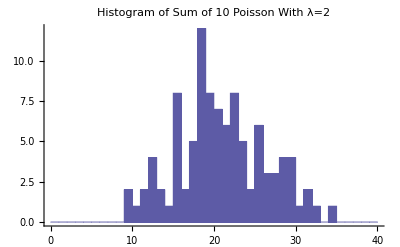

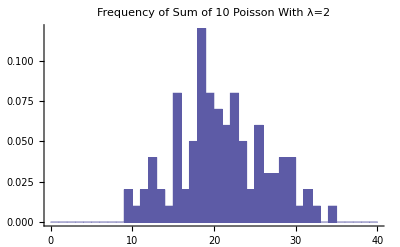

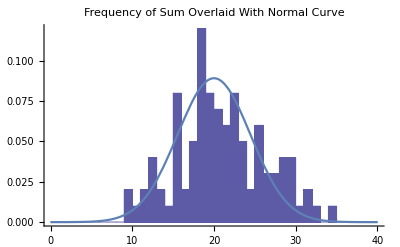

```mathematica
X:=Sum[Random[PoissonDistribution[2]],{10}]
Sample100=Table[X,100];
bcount=BinCounts[Sample100,{0,40,1}];
GeneralizedBarChart[Table[{.5+(i-1)*1,bcount[[i]],1},{i,1,40}],PlotLabel->"Histogram of Sum of 10 Poisson With λ=2"]
GeneralizedBarChart[Table[{.5+(i-1)*1,bcount[[i]]/(1*100),1},{i,1,40}],PlotLabel->"Frequency of Sum of 10 Poisson With λ=2"]
Show[GeneralizedBarChart[Table[{.5+(i-1)*1,bcount[[i]]/(1*100),1},{i,1,40}],PlotLabel->"Frequency of Sum Overlaid With Normal Curve"],Plot[1/√(40*Pi)*Exp[-(x-20)^2/40],{x,0,40},PlotRange->All]]
```

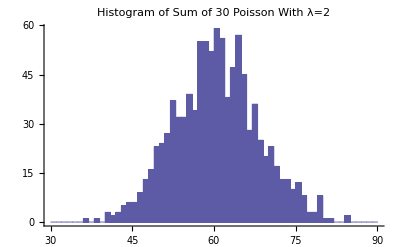

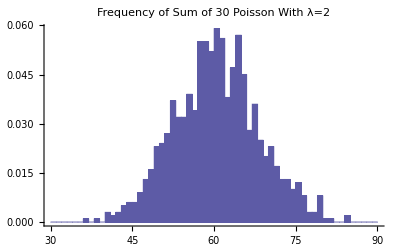

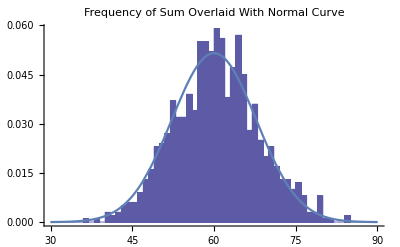

```mathematica
X:=Sum[Random[PoissonDistribution[2]],{30}]
Sample100=Table[X,1000];
bcount=BinCounts[Sample100,{30,90,1}];
GeneralizedBarChart[Table[{30.5+(i-1)*1,bcount[[i]],1},{i,1,60}],PlotLabel->"Histogram of Sum of 30 Poisson With λ=2"]
GeneralizedBarChart[Table[{30.5+(i-1)*1,bcount[[i]]/(1*1000),1},{i,1,60}],PlotLabel->"Frequency of Sum of 30 Poisson With λ=2"]
Show[GeneralizedBarChart[Table[{30.5+(i-1)*1,bcount[[i]]/(1*1000),1},{i,1,60}],PlotLabel->"Frequency of Sum Overlaid With Normal Curve"],Plot[1/√(120*Pi)*Exp[-(x-60)^2/120],{x,30,90},PlotRange->All]]
```

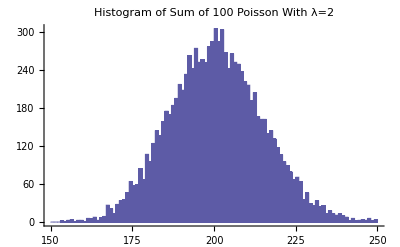

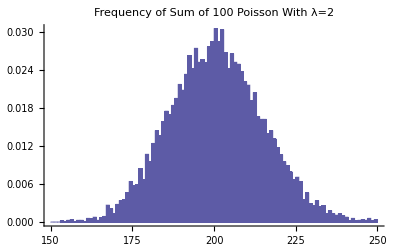

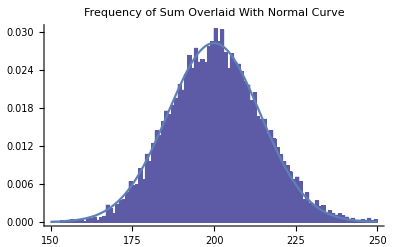

```mathematica
X:=Sum[Random[PoissonDistribution[2]],{100}]
Sample100=Table[X,10000];
bcount=BinCounts[Sample100,{150,250,1}];
GeneralizedBarChart[Table[{150.5+(i-1)*1,bcount[[i]],1},{i,1,100}],PlotLabel->"Histogram of Sum of 100 Poisson With λ=2"]
GeneralizedBarChart[Table[{150.5+(i-1)*1,bcount[[i]]/(1*10000),1},{i,1,100}],PlotLabel->"Frequency of Sum of 100 Poisson With λ=2"]
Show[GeneralizedBarChart[Table[{150.5+(i-1)*1,bcount[[i]]/(1*10000),1},{i,1,100}],PlotLabel->"Frequency of Sum Overlaid With Normal Curve"],Plot[1/√(400*Pi)*Exp[-(x-200)^2/400],{x,150,250},PlotRange->All]]
```

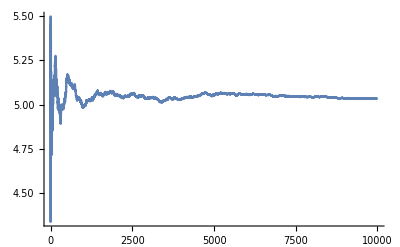

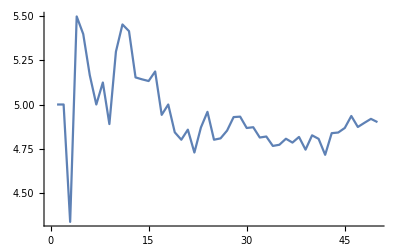

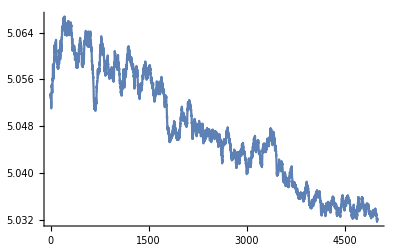

4.99952

```mathematica
data=Table[Random[PoissonDistribution[5]],10000];
sumdata=Accumulate[data];
average=Table[sumdata[[i]]/i,{i,1,10000}];
ListPlot[average,Joined->True,PlotRange->All]
ListPlot[Drop[average,{51,10000}],Joined->True,PlotRange->All]
ListPlot[Drop[average,{1,5000}],Joined->True,PlotRange->All]
s=0;n=1000000;sum=0;
For[i=1,i<4,i++,Do[r=Random[PoissonDistribution[5]];s=s+r,{i,1,n}];sum=sum+s;s=0]
Print[sum/n/3//N]
```